# Spline Pyramids

No need for imports, independent package

```mathematica
SetOptions[InputNotebook[],AutoGeneratedPackage->Automatic]
```

### Test Points

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0993805,0.90062,1.,1.,1.,1.,1.,1.,0.90062,0.0993805,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

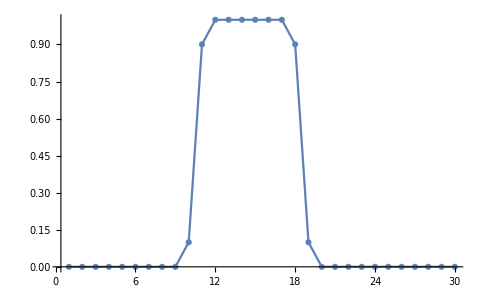

```mathematica
line=GaussianFilter[Table[If[11<= p<=18,1,0],{p,1,30}],1]
ListPlot[line,Joined->True,PlotMarkers->Automatic,PlotRange->All]
```

## Gaussian Kernel

Gaussian filter tap 5 where a={0.3, 0,6}

```mathematica
gaussianKernel[a_]:={1-a*2, 1,a*4,1,1-a*2}/4.0;

gaussianKernel::usage="
Gaussian filter tap 5 where a={0.3, 0,6}
";
```

### Test

```mathematica
gaussianKernel[0.3]
```

{0.1,0.25,0.3,0.25,0.1}

## next Pyramid’s level values

Takes values from any level and return the values of the next level
ADDS a value before and after, padding of 2 which become 1 due to averaging

```mathematica
pyrNextLevel[line_]:=Block[{d},(
d=ListConvolve[gaussianKernel[0.3],ArrayPad[line,2(* to get 1 extra value on each side *),"Fixed"]]
(*Mean/@Partition[d,2]*)



)];

pyrNextLevel::usage="
Takes values from any level and return the values of the next level
ADDS a value before and after, padding of 2 which become 1 due to averaging
";
```

### Test

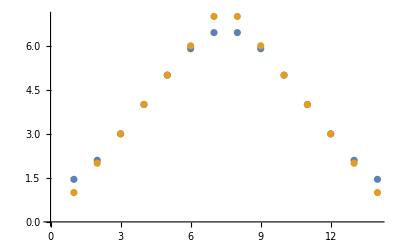

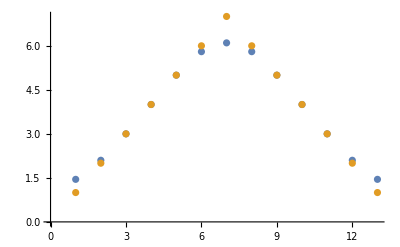

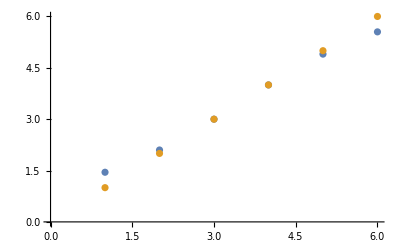

```mathematica
ListPlot[{pyrNextLevel[{1,2,3,4,5,6,7,7,6,5,4,3,2,1}],{1,2,3,4,5,6,7,7,6,5,4,3,2,1}}]
ListPlot[{pyrNextLevel[{1,2,3,4,5,6,7,6,5,4,3,2,1}],{1,2,3,4,5,6,7,6,5,4,3,2,1}}]
ListPlot[{pyrNextLevel[{1,2,3,4,5,6}],{1,2,3,4,5,6}}]
```

### Test

```mathematica
y=pyrNextLevel[line];
line
y
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0993805,0.90062,1.,1.,1.,1.,1.,1.,0.90062,0.0993805,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

{0.,0.,0.,0.,0.00496902,0.234938,0.765062,0.995031,0.995031,0.765062,0.234938,0.00496902,0.,0.,0.,0.,0.}

## Pyramid’s spline interpolation

create a spline for the line containing y values, and coords contains the x coordinates of the values
  actually, only the first and last coords are used...

```mathematica
functionGen[line_] := Block[{fline}, (

fline=ListInterpolation[line, {1,Length[line]}, Method -> "Spline", InterpolationOrder -> 3];
{fline,fline'}

)];

functionGen::usage="
create a spline for the line containing y values, and coords contains the x coordinates of the values
  actually, only the first and last coords are used...
";
```

## Pyramids generation

generate all pyramid lines
pyramid factor is hard-coded at 2
We assign coordinates 1..20 to a list of 20 values in line0.

```mathematica
pyrFuncGen[line0_,maxLevel_]:=Block[{y,x},(
functionGen[#]&/@NestList[pyrNextLevel,line0,maxLevel]
)];

pyrFuncGen::usage="
Input= [Points to interpolate, max target lvl]
Output= {maxlvl+1, {f, df}}
";
```

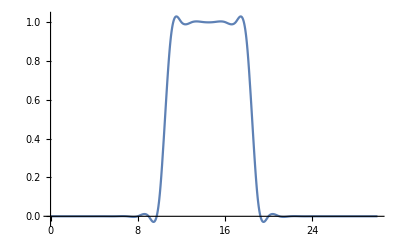
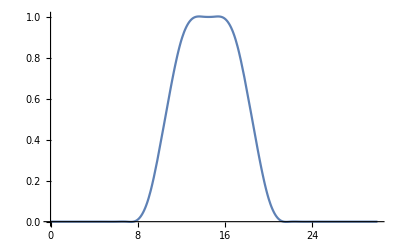
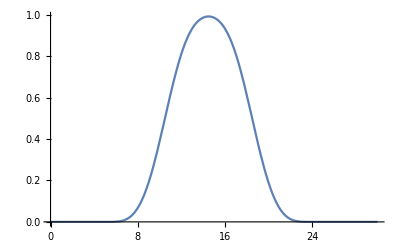
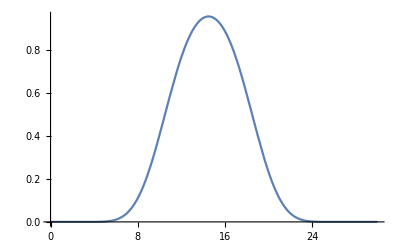

```mathematica
Plot[#[[1]][x],{x,0,Length[line]}]&/@pyrFuncGen[line,3]
```

### Test

{{InterpolatingFunction[…],InterpolatingFunction[…]},{InterpolatingFunction[…],InterpolatingFunction[…]},{InterpolatingFunction[…],InterpolatingFunction[…]},{InterpolatingFunction[…],InterpolatingFunction[…]}}

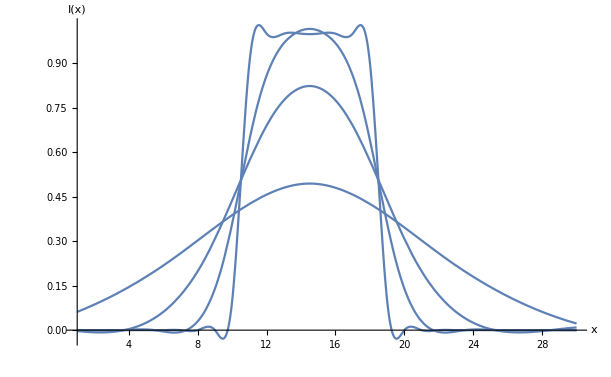

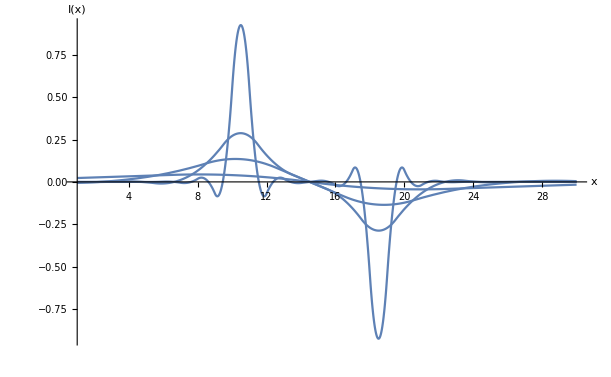

```mathematica
pyrf=pyrFuncGen[line,3]
fontsize=16;
Plot[#[[1]][x]&/@pyrf,{x,1,Length[line]},
PlotRange->All, 
AxesLabel->{Style["x",FontSize->fontsize,FontFamily->"Times", Italic],Style["I(x)",FontSize->fontsize,FontFamily->"Times", Italic]}]

Plot[#[[2]][x]&/@pyrf,{x,1,Length[line]},
PlotRange->All, 
AxesLabel->{Style["x",FontSize->fontsize,FontFamily->"Times", Italic],Style["I(x)",FontSize->fontsize,FontFamily->"Times", Italic]}]
```